## Лабораторная работа №23

# Изучение электропроводности и определение удельного сопротивления полупроводников

## Нехаев Александр 654 гр.

## Задачи

Ознакомиться с методикой проведения измерений.

Провести необходимые измерения для определения удельного сопротивления полупроводникового образца

Сделать выводы об однородности образца

## Ход работы

-Graphics-

Принципиальная схема двухзондового метода измерения удельного сопротивления полупроводникового образца.

Используя 4 контакта с проводником, проводим измерения с помощью компенсационного метода.

При смещении одного из зондов исследуем длину L=L_0-x. x смещаем по 0.25 мм.

Таблица 1. Полученные данные

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["data.xlsx"][[1]];
experiment=data[[3;;All,1;;3]];
experiment=Transpose[{Quantity[Around[experiment[[All,1]],0.01],"Millimeters"],Quantity[Around[experiment[[All,2]],0.1],"Milliamperes"],Quantity[Around[experiment[[All,3]],0.1],"Millivolts"]}];
Grid[Prepend[experiment,{"L", "I","U"}],Frame->All]
```

L | I | U
(0.0000.010) mm | (100.000.10) mA | (16.300.10) mV
(0.2500.010) mm | (100.000.10) mA | (14.600.10) mV
(0.5000.010) mm | (100.000.10) mA | (15.500.10) mV
(0.7500.010) mm | (100.000.10) mA | (14.500.10) mV
(1.0000.010) mm | (100.000.10) mA | (14.800.10) mV
(1.2500.010) mm | (100.000.10) mA | (14.000.10) mV
(1.5000.010) mm | (100.000.10) mA | (13.000.10) mV
(1.7500.010) mm | (100.000.10) mA | (14.100.10) mV
(2.0000.010) mm | (100.000.10) mA | (13.200.10) mV
(2.2500.010) mm | (100.000.10) mA | (12.100.10) mV
(2.5000.010) mm | (101.000.10) mA | (12.400.10) mV
(2.7500.010) mm | (101.000.10) mA | (9.500.10) mV
(3.0000.010) mm | (102.000.10) mA | (10.900.10) mV
(3.2500.010) mm | (101.000.10) mA | (11.400.10) mV
(3.5000.010) mm | (101.000.10) mA | (9.400.10) mV
(3.7500.010) mm | (101.000.10) mA | (9.800.10) mV
(4.0000.010) mm | (101.000.10) mA | (9.200.10) mV
(4.2500.010) mm | (101.000.10) mA | (8.400.10) mV
(4.5000.010) mm | (102.000.10) mA | (8.500.10) mV
(4.7500.010) mm | (102.000.10) mA | (7.800.10) mV
(5.0000.010) mm | (102.000.10) mA | (7.700.10) mV

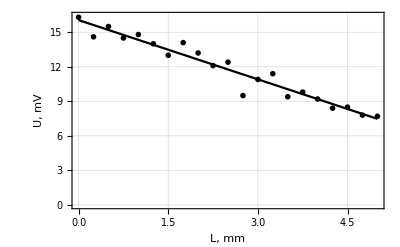

```mathematica
toPlot=Transpose[{experiment[[All,1]],experiment[[All,3]]}];
approx=LinearModelFit[Transpose[{data[[3;;All,1;;3]][[All,1]],data[[3;;All,1;;3]][[All,3]]}],x,x];
Show[ListPlot[Transpose[{experiment[[All,1]],experiment[[All,3]]}],PlotTheme-> "Detailed",FrameLabel->{"L, mm", "U, mV"}],Plot[approx["BestFit"],{x,0,5}]]
```

На графике наблюдается отклонение от линейной зависимости больше чем погрешность. Значит образец имеет неоднородности.

Параметры аппроксимации:

```mathematica
approx["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 16.055 | 0.281232 | 57.0881 | 1.01813×10^-22
x | -1.71532 | 0.0962261 | -17.826 | 2.55138×10^-13

Диаметр образца: d=6 мм ⇒ Находим площадь:

```mathematica
S=N[(π*Quantity[6,"Millimeters"]^2)/4]
```

28.2743 mm^2

Пусть

U_x - падение напряжения между зонами 2 и 3, U_эт - падение напряжения на эталонном сопротивлении

U_x/U_эт=R_x/R_эт; U_x=(ρ I_эт)/S L⇒k=(ρ I_эт)/S⇒ρ=k S/I_эт; I_эт=100 мА

Удельное сопротивление образца

ρ=k S/I_эт

При подстановке получаем:

```mathematica
ρ=Quantity[Around[-approx["BestFitParameters"][[2]],approx["ParameterErrors"][[2]]],"Millivolts"/"Millimeters"]*S/Quantity[100,"Milliamperes"];
UnitConvert[ρ,"Ohms"*"Millimeters"]
```

(0.4850.027) mm Ω

## Вывод

Изучили образец с помощью 4-х контактного метода. Получили зависимость U_x=f(x). По ней определили удельное линейное сопротивление. Зависимость имеет линейный вид с явными неоднородностями.